# Brezposelnost v državah OECD

Podatke pridobimo s spletne strani OECD in jih shranimo v Excelovi tabeli (CSV datoteko moramo z Excelom importati v XLSX). V spodnji tabeli so vsi obstoječi podatki za vse države članice OECD.

```mathematica
podatki=Import["C:\\Users\\katis\\ROM-projekt2\\podatki_OECD_brezposelnost.xlsx"][[1]]
```

{{LOCATION,INDICATOR,SUBJECT,MEASURE,FREQUENCY,TIME,Value},{AUS,HUR,TOT,PC_LF,A,1967.,1.875},{AUS,HUR,TOT,PC_LF,A,1968.,1.85},{AUS,HUR,TOT,PC_LF,A,1969.,1.8},{AUS,HUR,TOT,PC_LF,A,1970.,1.625},{AUS,HUR,TOT,PC_LF,A,1971.,1.925},{AUS,HUR,TOT,PC_LF,A,1972.,2.625},{AUS,HUR,TOT,PC_LF,A,1973.,2.325},65642,{EU27_2020,HUR,WOMEN,PC_LF,M,,8.1},{EU27_2020,HUR,WOMEN,PC_LF,M,,8.3},{EU27_2020,HUR,WOMEN,PC_LF,M,,8.2},{EU27_2020,HUR,WOMEN,PC_LF,M,,8.},{EU27_2020,HUR,WOMEN,PC_LF,M,,7.8},{EU27_2020,HUR,WOMEN,PC_LF,M,,7.7},{EU27_2020,HUR,WOMEN,PC_LF,M,,7.7}}
 |  |  |  |

Seznam kratic imen vseh članic OECD v seznamu:

```mathematica
kratice=#[[1]]&/@podatki//Rest//DeleteDuplicates
```

{AUS,AUT,BEL,CAN,CZE,DNK,FIN,FRA,DEU,GRC,HUN,ISL,IRL,ITA,JPN,KOR,LUX,MEX,NLD,NZL,NOR,POL,PRT,SVK,ESP,SWE,CHE,TUR,GBR,USA,CHL,EST,ISR,SVN,EU28,OECD,G-7,EA19,LVA,LTU,COL,EU27_2020}

```mathematica
oecdClanice=EntityList[EntityClass["Country","OrganizationForEconomicCooperationAndDevelopment"]]
```

{Australia,Austria,Belgium,Canada,Chile,Czech Republic,Denmark,Estonia,Finland,France,Germany,Greece,Hungary,Iceland,Ireland,Israel,Italy,Japan,Luxembourg,Mexico,Netherlands,New Zealand,Norway,Poland,Portugal,Slovakia,Slovenia,South Korea,Spain,Sweden,Switzerland,Turkey,United Kingdom,United States}

Seznam držav OECD skupaj z kratico in slovenskim imenom (to tabelo smo morali sestaviti ročno)

```mathematica
seznamOECD=
```

```mathematica
SLOimena={"Avstralija","Avstrija","Belgija","Kanada","Češka","Danska","Finska","Francija","Nemčija","Grčija","Madžarska","Islandija","Irska","Italija","Japonska","Koreja","Luksemburg","Mehika","Nizozemska","Nova Zelandija","Norveška","Poljska","Portugalska","Slovaška","Španija","Švedska","Švica","Turčija","Velika Britanija","ZDA","Čile","Estonija","Izrael","Slovenija","Članice EU", "Članice OECD","Članice G7","EA19","Latvija","Litva","COL","Članice EU brez V. Britanije"};
```

Seznam držav in kratice v istem vrstnem redu:

```mathematica
kratice={"AUS","AUT","BEL","CAN","CHE","CZE","DNK","EST","FIN","FRA","DEU","GRC","HUN","ISL","IRL","ISR","ITA","JPN","LUX","MEX","NLD","NZL","NOR","POL","PRT","SVK","SVN","KOR","ESP","SWE","CHE","TUR","GBR","USA"};
```

```mathematica
slovar=Table[oecdClanice[[i]]->kratice[[i]],{i,Length[kratice]}]
```

{Australia→AUS,Austria→AUT,Belgium→BEL,Canada→CAN,Chile→CHE,Czech Republic→CZE,Denmark→DNK,Estonia→EST,Finland→FIN,France→FRA,Germany→DEU,Greece→GRC,Hungary→HUN,Iceland→ISL,Ireland→IRL,Israel→ISR,Italy→ITA,Japan→JPN,Luxembourg→LUX,Mexico→MEX,Netherlands→NLD,New Zealand→NZL,Norway→NOR,Poland→POL,Portugal→PRT,Slovakia→SVK,Slovenia→SVN,South Korea→KOR,Spain→ESP,Sweden→SWE,Switzerland→CHE,Turkey→TUR,United Kingdom→GBR,United States→USA}

Za vsakega od zgornjih podatkov nas zanima le ime članice, “subject” (moški/ženske/vsi), leto in stopnja brezposelnosti.

```mathematica
podatkiOdbrani={#[[1]],#[[3]],#[[6]],#[[7]]}&/@Rest[podatki]
```

{{AUS,TOT,1967.,1.875},{AUS,TOT,1968.,1.85},{AUS,TOT,1969.,1.8},{AUS,TOT,1970.,1.625},{AUS,TOT,1971.,1.925},{AUS,TOT,1972.,2.625},{AUS,TOT,1973.,2.325},{AUS,TOT,1974.,2.7},{AUS,TOT,1975.,4.925},{AUS,TOT,1976.,4.75},{AUS,TOT,1977.,5.65},{AUS,TOT,1978.,6.44253},{AUS,TOT,1979.,6.2655},65630,{EU27_2020,WOMEN,,7.},{EU27_2020,WOMEN,,6.8},{EU27_2020,WOMEN,,6.8},{EU27_2020,WOMEN,,6.8},{EU27_2020,WOMEN,,7.2},{EU27_2020,WOMEN,,7.6},{EU27_2020,WOMEN,,8.1},{EU27_2020,WOMEN,,8.3},{EU27_2020,WOMEN,,8.2},{EU27_2020,WOMEN,,8.},{EU27_2020,WOMEN,,7.8},{EU27_2020,WOMEN,,7.7},{EU27_2020,WOMEN,,7.7}}
 |  |  |  |

Naslednja funkcija bo v odvisnosti od države vrnila seznam parov {leto, brezposelnost}. Pri tem vzamemo le subject = “TOT” ter tiste podatke, ki imajo podano tudi leto.

```mathematica
podatkiZaDrzavo[drzava_]:=Module[{sel},sel=Select[podatkiOdbrani,#[[1]]==(drzava/.slovar)&&#[[2]]=="TOT"&&#[[3]]≠""&];Table[{sel[[i]][[3]],sel[[i]][[4]]},{i,Length[sel]}]]
```

```mathematica
podatkiZaDrzavo[Entity["Country","Slovenia"]]
```

{{1996.,6.89167},{1997.,6.91667},{1998.,7.36667},{1999.,7.40833},{2000.,6.74167},{2001.,6.19167},{2002.,6.34167},{2003.,6.7},{2004.,6.34167},{2005.,6.54167},{2006.,5.99167},{2007.,4.85833},{2008.,4.39167},{2009.,5.89167},{2010.,7.275},{2011.,8.20833},{2012.,8.89167},{2013.,10.1583},{2014.,9.74167},{2015.,9.},{2016.,8.00833},{2017.,6.6},{2018.,5.125},{2019.,4.45},{2020.,4.89167}}

Naslednja funkcija za seznam držav izriše njihove podatke.

```mathematica
Narisi[{drzava_}]:=ListLinePlot[podatkiZaDrzavo[drzava],ImageSize->Large,PlotLabel->"Stopnja brezposelnosti v državi: "<>drzava["Name"]]
Narisi[seznam_]:=ListLinePlot[podatkiZaDrzavo/@seznam,PlotLegends->(#["Name"]&/@seznam),ImageSize->Large,PlotLabel->"Stopnja brezposelnosti v državah: "<>StringJoin[Table[seznam[[i]]["Name"]<>If[i==Length[seznam],"",", "],{i,Length[seznam]}]]]
```

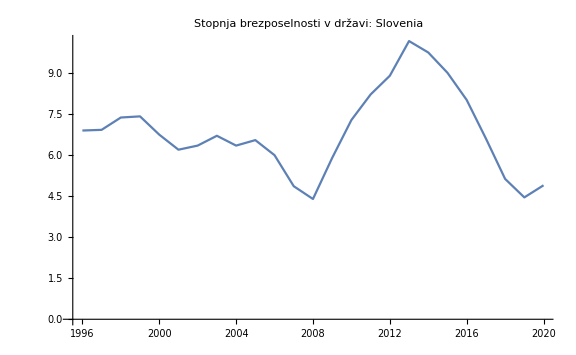

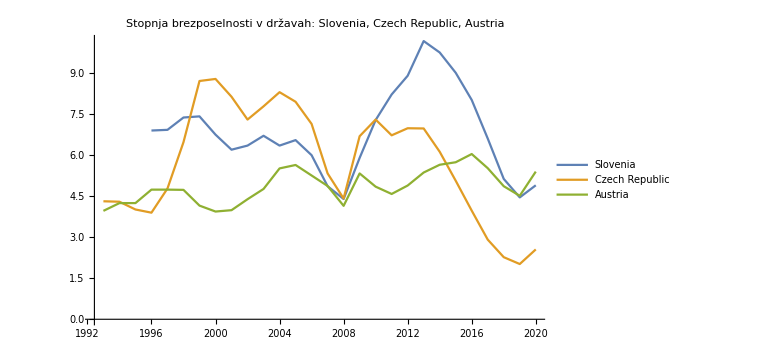

```mathematica
Narisi[{Entity["Country","Slovenia"]}]
Narisi[{Entity["Country","Slovenia"],Entity["Country","CzechRepublic"],Entity["Country","Austria"]}]
```